# Mathematica Introduction

Week 1 of Introduction to Computational Biology Labs

At this point you should inform your teaching assistant if you lack algebra or calculus knowledge. Don’t wait until the end of the course when you get a bad grade. When that happens, you are stuck with that grade :-( . 
Additionally, don’t forget that google can be a good friend :-).

## Background

This notebook functions as a introduction to Mathematica programming and will give you the basic knowledge to start using Mathematica for your modelling exercises. It will also shortly give you a background of the language.  
Blue text are links to additional information.

Why use Mathematica

There are different reasons why we want to use and introduce you to Mathematica in this course. To be honest, there is nothing that Mathematica can do that other programming languages cannot. On top of this, other great programming languages are open source and free. However, many things in Mathematica can be done with a lot less effort and time due to the already built in generic and specific functionalities. The very high level of the language also means we can focus more on the problem at hand, rather than thinking and spending time on the implementation. This is very useful in biology, since biological problems can already be complex enough without needing to think about complex implementations and programming.  

Here are some more reasons to consider Mathematica as a programming language: 

1. Multiparadigm language. Not every problem can be approached with one style. Mathematica supports many programming paradigms, including procedural, functional, rule-based and pattern-based.  

2. Interactivity. The front-end of Mathematica allows another layer of interactivity to your programming. You are able to visualize both input and output, while also documenting everything. 

3. Great visualizations. Great dynamic and (interactive) visualization possibilities. 

4. Built-ins. Including built-in functions, toolboxes and data. The data is curated data of all kinds, continuously updated and expanded. 

5. Relatively easy to learn. 
    
There are many more reasons to use Mathematica. However, in an attempt to not make this sound like an advertisement I will stop here. Feel free to explore their website. In the end, you can (if you have not already) add another very powerful programming language to your arsenal.

Mathematica environment

Mathematica consists of two parts, the Kernel aka the computational engine and the Front end aka the Interface. The kernel and front-end can both run on the same computer (like on your home desktop/laptop, or the kernel can run on a (powerful) server with the front-end running on a local host (like in the lab rooms). So when you enter and input on the front-end, the kernel will be contacted and will process the input. The kernel will then send the output back to the front-end.
The front-end is also called a notebook, which we will discuss in more detail in the next section.

Notebook structure

Currently, you are reading text in the notebook. You can see the notebook as a folded piece of paper, which can contain as many fold and as organized as you like. The ‘folds’ are called cells. Cells can be enclosed by other cells and can be closed and opened at will. The cells are represented by brackets on the far right of this page. 
The hierarchical structure of a cell group is indicated by the layering of the cells. Mathematica groups cells according to cell styles. For instance, a subsection is automatically grouped with text cells below the subsection cell. For instance, the cell where this text is written is a grouped with the “Notebook structure” subsection cell. The “Notebook structure” section is grouped with the “Mathematica environment” section etc... On top of the hierarchy is the “Mathematica Introduction” cell.
Double clicking on a cell will open and close it. A closed cell is marked by a darkened corner at the bottom (try it by double clicking a cell that has a group of cells inside it). Like the cell below.

#### Cell properties

The properties of a cell tell Mathematica how to deal with the cell contents. If you hover your mouse pointer over an empty part of the notebook a horizontal text cursor will appear. By default, if you make a new cell (by clicking on the empty part of the notebook), the cell will become an calculation “Wolfram language” input cell (which we will just call input from now on). If you click on the little cross symbol (+) on the left you can choose if you want to change the cell style to for instance plain text.   
If the cell is an input cell with some type of calculation, you can evaluate the cell. This will send the calculation to the kernel. You can see if it is an input cell by looking at the cell brackets (white upper corner), like below. You evaluate the cell by clicking on it (or after writing it) pressing Shift, followed by Enter. 
Try it:

```mathematica
1 + 1
```

2

You should notice a few things. First, Mathematica assigns in sequence a number to each of the cells it evaluates. This is useful to address previous results in a longer calculation. Next notice the output cell that was created automatically. The input and output are automatically grouped. 
You can check what kind of cell it is (and change the type) also by checking the menu Cell > Convert To. The StandardForm is the standard input and output, which can BOTH be edited. Changing an output from StandardForm to OutputForm will make the output un-editable. If you want to produce printable notebooks, the TraditionalForm produces a output with traditional mathematical notations. Check it out below (and notice the different cell brackets).

```mathematica
(x^3+y^2+z)/(x^2-y)
```

(x^3+y^2+z)/(x^2-y)

```mathematica
(x^3+y^2+z)/(x^2-y)
```

(x^3+y^2+z)/(x^2-y)

```mathematica
3    2
x  + y  + z
-----------
   2
  x  - y
```

```mathematica
(x^3+y^2+z)/(x^2-y)
```

```mathematica
(x^3+y^2+z)/(x^2-y)
```

#### Palettes

Input can be organized using the Palettes menu. Here you can find Greek letters, matrices, mathematical formulations etc. Palettes can also be installed from external sources to add additional functionality. Go experiment a little.

Getting help in Mathematica

Mathematica is very large, with a great amount of functions and possibilities. Even the most experienced Mathematica users need help once in a while. So knowing how to get help is part of the learning process. The Mathematica website will provide you with many additional manuals/documentation. This can also be find under the Help menu > Wolfram Documentation. Additional useful stuff can be found in this Help menu. Use the shortcut Cmd+ Shift + F (Mac) to find a selected word/function (or look at what shortcut you need for this from the Help menu). 
Something that might also be useful is the Help > Why the Beep?... . If something goes wrong during an evaluation, you will hear a beep. Using the Why the Beep? function can help you sort this out. 
The Options[...] function can be used to find the option available for a function and the question mark symbol (?) can tell you what kind of object it is, e.g.:

```mathematica
Options[Plot]
? Plot
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

Let us not forget Google! Man’s second best friend.

## The basics in Mathematica

These are the essential basics you need to understand Mathematica before using it.

Input and output

Input can be purely text based (which was the only option in the first Mathematica versions)

```mathematica
Power[x,2]
```

However, (now) it is also possible to use shorthand notation:

```mathematica
x^2
```

x^2

```mathematica
(x^2-1)/(y+3)
```

Another notation uses the ctrl button, e.g. x Ctrl + ^ and x Ctrl + _. You can also use the Palettes.

```mathematica
x^2
Subscript[x, 2]
```

The output of a cell can be suppressed by a semicolon (;) when evaluating a cell. This can also be used to separate statements on a line

```mathematica
1+3;2+4
```

6

The output of a previous calculation can also be recalled and reused with the “%” sign.

```mathematica
% *3
```

18

#### Syntax colors

Be aware of the syntax colors. 
For instance, blue means a parameter/symbol that is not recognized or used by Mathematica, i.e. undefined symbol. Functions are also blue. Dark Grey and Grey are strings and comments respectively.  Errors are largely given in red or pink.    
When you define a function with “x_”, the x_ will turn green. This is now a function definition, which will be later explained in more detail.

```mathematica
(*Comment about something*)

a = "String assigned to a symbol"

fac[x_]:=x fac[x-1]
```

You can adjust these default colors or look which colors are used for what in Mathematica > Preferences > Appearance.

Notational convention and principles

#### Built-in names/functions

The names of all Built-in functions, options, variable and constants start with CAPITAL letters. If it consists of two words, both words begin with a capital letter. Abbreviations are rarely used by Mathematica, unless they are well known. Some abbreviations include: Abs, Cos, Sin, Det, etc. ... Other functions include: Eigenvalues, FindRoot, Integrate.

#### Naming functions, symbols, expression etc.

Variables can be either symbols or normal expressions. The names of symbols can contain letters and numbers, but cannot start with a number nor contain special characters (like the underscore). Using the Head function can help you check whether a symbol is legitimate. 
Starting your symbols and functions with a small letter will ensure you will have no conflicts with the many Mathematica symbols and functions.  

A common problem with beginner Mathematica users is that they are trying to use variables that they already have assigned values to, causing calculations to go wrong. Be careful with this when switching between assignments. Either use different variable names or clear, clear and clear!
Functions you can use to clear a variable are Clear, ClearAll and Remove. Please take a loot at how they differ. A short version of the clear function is given in the example below. We assign a value to x (4), when we call x it will show 4. Clearing x and then calling it again, will give x the value x.

```mathematica
x=4
x
x=.
x
```

When you want to remove all defined symbols so that their names are no longer recognized it can be useful to use Remove[“Global`*”]. To remove all values, definitions, attributes it is more appropriate to use ClearAll["Global'*"]. You can also use this for single values etc. Using a question mark (?) will print all the definitions for a symbol.

```mathematica
a = 1;
? a
```

```mathematica
a=.
?a
```

#### Characters

Characters can be used to make the text/code more readable and understandable. You can use the “esc” (escape) button for this or this list. A few examples:

Character	Input*			Esc shortcut*
∫		\ [Integral] 	 		Esc int Esc
∂		\ [PartialD]			Esc pd Esc 
ⅆ		\ [DifferentialD] 		Esc dd Esc
π		\ [Pi]		 		Esc pi Esc 	or   Esc p Esc		Built in constant
∞		\ [Infinity]	 		Esc inf Esc
σ		\ [Sigma]			Esc sigma Esc
Δ 		\ [CapitalDelta]	 		Esc D Esc 	or  Esc Delta Esc 
ⅈ		\ [ImaginaryI]	 		Esc ii Esc
ⅇ		\ [ExponentialE]		Esc ee Esc				 	Built in constant
⟦		\ [RightDoubleBracket]	Esc [[ Esc
* Don’t use the space between slash (\) and [word] andc Esc word Esc. The slash is used here to stop the symbol from appearing.
The escape button will look like  when pressed.

#### Mathematical notations

Mathematica uses symbols for arithmetic notations, but can also use words:

Symbol		Word
+    		Plus
-    		Subtract
*    		Times
/    		Divide
^    		Power
!    		Factorial
==		Equal
<    		Less
<=   		LessEqual
>    		Greater
>=   		GreaterEqual

#### Brackets

Mathematica adopts slightly different conventions from other programming languages with brackets.

Bracket                       Purpose                     	       Examples
(...)			Grouping                  		(a + b)/(c + d)
f[...]       		Arguments of function         	Sin[2 Pi x]
{...}	       		Vectors, matrices, and lists     {x, 2 x, 3 x}
v[[...]] or v⟦...⟧        	Indexing                   		m⟦3⟧, m[[1,2]]
(* ... *)  		Commenting                	(* a comment *)

#### Understanding expressions/functions

As already described above, every built-in function has a literal string equivalent. By using the FullForm command you can see the internal representation of any object/expression as seen by the kernel.
All expressions are trees. With the command TreeForm you can see this clearly. Since it is a tree, you can index and access the subexpression.

```mathematica
TreeForm[z*Sin[x+y]]
a = z*Sin[x+y]
FullForm[a]
```

We can then use indexing to access internal parts of the expression and deconstruct the expression if wanted, starting at the head of the tree. For instance:

```mathematica
{a⟦0⟧,a⟦1⟧,a⟦2⟧,a⟦2,0⟧, a⟦2,1⟧}
```

#### Pattern-matching and rule substitutions

A fundamental principle is pattern-matching, a system to match rules and expressions. Without it, Mathematica wouldn’t know when to apply. A typical rule looks like:

```mathematica
c-> d
```

The arrow can be coded with a simple “->”. The “c” and “d” are expressions. This rule says: whenever “c” is encountered, replace it by “d”.

```mathematica
{c,d,e,e,d,c}/.c->d
```

The “/.” symbol is a rule replacement command. You can use also use this for replacing something in an expressions, for instance:

```mathematica
2x/.x->3
c-x/.x->%
```

A pattern is essentially any expression with some part replace by “blank” (Blank[]). It is a placeholder for any expression. The literal equivalent of Blank is the underscore “_” symbol, which we encountered before. For instance, f[x_] means, f[anything].

```mathematica
f[x_]:=x^2
{f[2],f["hello"], f["biology"]}
```

“x_” is the simplest pattern. There are more complex patterns, with even conditions attached to them. This can ensure that only patterns will match when certain conditions are met. You can look for more info on constraints on patterns on and here fore more info on rules and patterns, more patterns and transformation rules.

#### Assignments

There are two assignment commands in Mathematica, which you might have seen allready in some examples above. The two types are immediate and delayed assignments. The immediate sign is the equal sigh “=”. The delayed assignment is the equal sign with a semicolon “:=”. The right hand side of this assignment will not be evaluated at the moment of assignment, but re-evaluated every time when the left hand side appears somewhere.

#### Small summary on rules/assignments

rule | evaluated | unevaluated
lhs=rhs | rhs | lhs
lhs:=rhs |   | lhs,rhs
expr/.lhs→rhs | expr,lhs,rhs |  
expr/.lhs:>rhs | expr,lhs | rhs

## Using Mathematica

Graphics

Mathematica has powerful built-in graphics functions in both 2D and 3D. To generate a plot of f as a function of x, x_min to x_max:

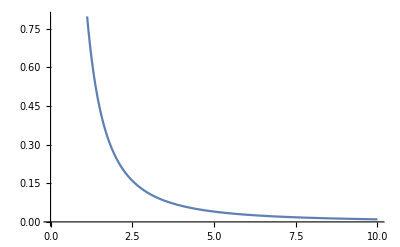

```mathematica
Plot[1/x^2,{x,0,10}]
```

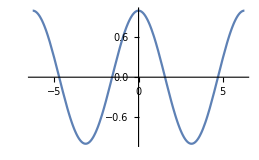

```mathematica
Plot[Cos[x],{x,-2π, 2π}]
```

```mathematica
Plot3D[(x y)/(x^2+y^2+.1),{x,-1,1},{y,-1,2}]
```

-Graphics3D-

Many commands can have extra options to be specified, also the plotting functions. An example is the slight variation on the previous example using one of the options for Plot3D. Rather than having Mathematica re-computing all of the points on the graph, we can use the Show[%, options] to change the display options of the previous graphic. If you know the options you want to have beforehand you can add them immediately to the plot functions.

```mathematica
Show[%,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Show[%,PlotLabel->"Mathematica Surface"]
```

-Graphics3D-

Parametric curves can also be easily drawn.

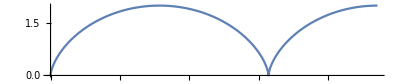
c -Graphics-

```mathematica
ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,3 π},AspectRatio->2/(3 π)]c
```

```mathematica
r[z_]:=√(1+z^2)
ParametricPlot3D[{r[z] Cos[theta],r[z] Sin[theta],z},{z,-2,2},{theta,0,2 π}]
```

-Graphics3D-

Algebraic computations

You can do symbolic computations, including algebra and calculus. Mathematica can also learn any computational rules you want to teach it.

#### Polynomials

Expanding and factoring polynomials can be done with the Expand and Factor functions. The latter being a much more readable and simpler form.

```mathematica
Expand[(9 (2+x) (x+y)+(x+y)^2)^3]
Factor[%]
```

5832 x^3+9720 x^4+5400 x^5+1000 x^6+17496 x^2 y+30132 x^3 y+17280 x^4 y+3300 x^5 y+17496 x y^2+32076 x^2 y^2+19494 x^3 y^2+3930 x^4 y^2+5832 y^3+12636 x y^3+8802 x^2 y^3+1991 x^3 y^3+972 y^4+1242 x y^4+393 x^2 y^4+54 y^5+33 x y^5+y^6

(x+y)^3 (18+10 x+y)^3

#### Differentiation and Integration

Partial differential equations can be inputted in multiple ways (see Basics of Mathematica section > Characters or use the Palettes). The partial derivative of ∂f/∂x with characters:

```mathematica
D[(x^3+x-1)/(x^2-1), x]
```

(1+3 x^2)/(-1+x^2)-(2 x (-1+x+x^3))/((-1+x^2)^2)

, with function notation for partial differentials.

```mathematica
D[(x^3+x-1)/(x^2-1),x]
```

(1+3 x^2)/(-1+x^2)-(2 x (-1+x+x^3))/((-1+x^2)^2)

Here it is useful to introduce the Simplify function that will return the simplest form of an expression, in this case the previously given partial derivative:

```mathematica
Simplify[%]
```

(-1+2 x-4 x^2+x^4)/((-1+x^2)^2)

You can also calculate (in)definite integrals using both characters and function notations:

```mathematica
∫x √(x^2+1) ⅆx
```

1/3 (1+x^2)^(3/2)

To give the upper limit use Ctrl + % and for the lower limit use Ctrl + _

```mathematica
∫_0^2 x √(x^2+1) ⅆx
```

1/3 (-1+5 √5)

```mathematica
Integrate[x √(x^2+1),x]
```

1/3 (1+x^2)^(3/2)

```mathematica
Integrate[x √(x^2+1),{x,0,2}]
```

1/3 (-1+5 √5)

To get the numerical approximation of the integral:

```mathematica
NIntegrate[x √(x^2+1),{x,0,2}]
```

3.39345

#### Power series expansion

As an example let’s look at the Taylor polynomial around x = 0 (also called Maclaurin polynomial), computed to the 20th degree with the Series function.

```mathematica
Series[(x^2-1)Sin[x^2],{x,0,20}]
```

-x^2+x^4+x^6/6-x^8/6-x^10/120+x^12/120+x^14/5040-x^16/5040-x^18/362880+x^20/362880+O[x]^21

```mathematica
Series[f[x],{x,q,2}]
```

f[q]+f'[q] (x-q)+1/2 f''[q] (x-q)^2+O[x-q]^3

#### Limits

With the Limit function with.

```mathematica
Limit[(1+1/x)^x,x->∞]
```

ⅇ

```mathematica
Limit[Cos[x],x->0]
```

1

Numerical calculations

In the first examples you saw that you can do arithmetic with Mathematica like using a normal calculator. However, Mathematica can additionally give you exact results.

```mathematica
5^1000
```

933263618503218878990089544723817169617091446371708024621714339795966910975775634454440327097881102359594989930324242624215487521354032394841520817203930756234410666138325150273995075985901831511100490796265113118240512514795933790805178271125415103810698378854426481119469814228660959222017662910442798456169448887147466528006328368452647429261829862165202793195289493607117850663668741065439805530718136320599844826041954101213229629869502194514609904214608668361244792952034826864617657926916047420065936389041737895822118365078045556628444273925387517127854796781556346403714877681766899855392069265439424008711973674701749862626690747296762535803929376233833981046927874558605253696441650390625

The numerical function N can help you get the approximate result to the accuracy you require. Remember the NIntegrate function, which is the numerical solution of the integration.

```mathematica
N[5^1000,4]
```

9.333×10^698

```mathematica
N[Pi,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

Complex numbers can also be handled, using the ⅈ or ⅉ character for imaginary numbers.

```mathematica
ⅈ^2
```

-1

i^2

```mathematica
(4+3ⅈ)^2
```

You can use the documentation center to find a function you need. Here are some common functions:

N[]
Sqrt[x]
Exp[x]
Log[x]
Log[b,x]
Sin[x], Cos[x], Tan[x]
ArcSin[x], ArcCos[x], ArcTan[x]
Abs[x]
Round[x]
Mod[n, m]
Random[]
Max[x, y, ...], Min[x, y, ...]
FindRoot[]
FactorInteger[n]
RealDigits[r]
IntegerDigits[n]

Solving Equations, ODEs and PDEs.

Let us now solve some problems in more detail with what we have learned so far. Mathematica has a set of functions to solve different problems, such as Solve, DSolve, NDSolve with the latter two for ODEs and PDEs. 
Look at the following examples to understand how to solve a problem and then use/retrieve the solutions using indexing and lists.

```mathematica
a=.;x=.;
x^3-7 x^2+3 a x==0
sol1 = Solve[%,x] (*Solves symbolically*)
ineedthis={sol1⟦1⟧, sol1⟦2⟧}
ineedthismore = sol1⟦1⟧⟦1⟧
```

3 a x-7 x^2+x^3==0

{{x→0},{x→1/2 (7-√(49-12 a))},{x→1/2 (7+√(49-12 a))}}

{{x→0},{x→1/2 (7-√(49-12 a))}}

x→0

Or immediately solve the function like this:

```mathematica
Solve[x^5+2 x+1==0,x]
```

{{x→Root[1+2 #1+#1^5&,1]},{x→Root[1+2 #1+#1^5&,2]},{x→Root[1+2 #1+#1^5&,3]},{x→Root[1+2 #1+#1^5&,4]},{x→Root[1+2 #1+#1^5&,5]}}

Oops...When this happens, it means that no explicit algebraic form could be found and only the symbolic result it given. In this case:

```mathematica
N[%]
```

Or if you are only interested in the numerical form the next example is a lot faster. This works for polynomial equations. However, keep in mind that NSolve is not suited for more general equations and therefore FindRoot must be used. FindRoot can be used on two equations simultatiously.

```mathematica
NSolve[x^5+2 x+1==0,x]
```

```mathematica
FindRoot[{Sin[x]==x-y,Cos[y]==x+y},{x,1},{y,0}]
```

Let’s try multiple equations...

```mathematica
a=.;b=.;c=.;
sol2=Solve[{a x+b y==0,x+y==c},{x,y}](*Solves symbolically*)
```

For solving differential equations you can use the DSolve function that finds the symbolic solution to the differential equations. Finding exact symbolic solutions of PDEs is a difficult problem, but DSolve can solve most first-order PDEs. 
We take as an example: (ⅆ^2 y)/(ⅆ x^2)=1+k y, we want to solve for the function y with independent variable x. This finds the general solution for a given ODE. A rule for the function that satisfies the equation is returned:

```mathematica
DSolve[y''[x]==1+k y[x],y[x],x]
```

{{y[x]→-1/k+ⅇ^(√k x) C[1]+ⅇ^(-√k x) C[2]}}

DSolve::dvnoarg: The function x appears with no arguments.

DSolve[x'[t]==C x,x[t],t]

Notice the notation with a double prime to annotate the second derivative. You can either use two single primes or superscript an Escape shortcut with two single primes: Esc ‘’ Esc. The dependent variable y is denoted as y[t]. 
You can also add an initial condition to get the particular solution (check the documentation). 
Differential equations can also be solved numerically with the NDSolve function. The solution will be given as an interpolation function that can be used in for instance a plot:

```mathematica
NDSolve[{y''[x]+Sin[x]^2 y'[x]+y[x]==Cos[x]^2,y[0]==1,y'[0]==0},y,{x,0,20}]
Plot[y[x]/.%,{x,0,20}, AxesLabel->{x,y[t]}]
```

Now let us look at a PDE: 2(∂y(x,t))/(∂x)+(∂y(x,t))/(∂t)=0. Using D to take the derivatives and DSolve we can solve the equation:

```mathematica
pde1 = D[y[x,t],t]+2D[y[x,t],x]==0 (*Set up the pde*)
solve1 = DSolve[pde1,y[x,t],{x,t}] (*Solve function y[x,t] over independent variable x and t.*)
```

While the general solution of ODEs involve arbitrary constants (C[i]), the general solution of a PDE involves arbitrary functions (also labeled C[i]). Adding a initial condition like y[0,t] = sin(t) is done like this:

```mathematica
solve2 = DSolve[{pde1,y[0,t]==Sin[t]},y[x,t],{x,t}]
```

Lists and Matrices

#### Lists and manipulations

Lists ({...}) are important objects in Mathematica and can be used for many different things. They already have been used in various examples in the previous sections (such as in the Plot and Solve functions). You can perform arithmetic operations, apply mathematical functions and assign variables to the list.

```mathematica
q = {1,2,4,5}
q+12
q-{1,1,2,2}
Log[q]//N (* The double slash is a Postfix form, which is this case is needed to get the numerical answer*)
```

Manipulating (elements) of a list can be done using the brackets [[...]] or Part function. You have seen this already briefly in previous sections. The following examples will show you what you can do:

```mathematica
list1={1,2,3,6,7,8} (*a list*)
list1⟦1⟧(*extract first element, notice we do not start counting at 0*)
list1⟦{4,5,6}⟧(*extracting part (element 4, 5 and 6) of the list*)
list1⟦2⟧=9 (*Replace element two with other value*)
list1
(*reset list*)  
list1=. 
list1
```

A list can also be made using different functions, such as Range:

```mathematica
Range[4,10]
```

A “list in a list” manipulations.

```mathematica
list2 = {{0,0},{1,2},{3,4},{5,6}}
list2⟦1⟧
list2⟦2⟧
list2⟦2⟧⟦1⟧
list2⟦2;;⟧
```

The “;;” symbol means the span of the elements i through j (i;;j).

#### Tables of values

Using the table function also a matrix can be made, now providing an additional argument. Basic algebraic calculations can the be performed, like calculating the determinant with Det function.

```mathematica
table1 =Table[x^2 j+2i, {i,2},{j,2}]
table2 = {{4,7,6},{3,1,2},{9,1,4}}
det1 = Det[table1]
det2 = Det[table2]
```

```mathematica
m1=({{x, z}, {y, x}})(*using the basic math assistant palette*)
det3=Det[m1] 
trans1 = Transpose[m1]
inver1 = Inverse[m1](*if determinant is non-zero the inverse can be calculated*)
```

MatrixForm is a function to pretty print matrices (it cannot be used for calculations). Making a matrix can be done with the MatrixForm function and supplying it with a list of lists {i, i+1, i+2, ...} with i beeing a list and the row of the matrix. We can then perform some basic algebraic computations.

```mathematica
mt = MatrixForm[trans1]
mi = MatrixForm[inver1]
mid = MatrixForm[Simplify[m1.inver1]] (*notice the Simplify function and what happens if you remove it*)
```

There are many other functions to construct different types of matrices. Here is a list of other functions that can be used on lists and matrices, their names are self explanatory:

Array[a,n] or Array[a, {n,m}]
Range[n]
Length[list]
ColumnForm[list]
Dimensions[list]
MatrixForm[list]
MatrixPower[m,n]
Inverse[m]
Det[m]
Transpose[m]
Eigenvectors[m]
Eigenvalues[m]

Getting parts
First[list]
Last[list]
Part[list,n]
Take[list,n]
Rest[list]
Drop[list,n]

Rearrange
Sort[list]
Union[list]
Reverse[list]
RotateLeft[list,n]
RotateRight[list,n]

## Programming in Mathematica

Mathematica is also a high-level programming language with capabilities to iterate, loop, and use user-defined functions etc. We will go through more advanced programming styles in the following sections and give paradigm examples. Let us first at a function that will be useful to have before doing this.

#### Modules

The Module function allows you to set up local variables with names that are local to this specific module and creates new symbols to represent each of them every time it is called.

```mathematica
t = 17
Module[{t},t=8;t]
t
```

#### Booleans and conditionals

Boolean Computations and conditionals are essential in any programming problem.

#### Interactive graphics

Graphics/plots can be programmed to be interactive. Functions that are used often for this are Manipulate and Animate.

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{a,1,4},{b,0,10}]
Animate[Plot[Sin[a x+b],{x,0,6}],{a,1,4},{b,0,10},AnimationRunning->True]
```

Functional programming

If we do functional operations such as:

```mathematica
NestList[f,x,4]
```

we have to specify a function to apply and we have used the name of the function to specify the function.
The functional programming paradigm is very developed in Mathematica. Here we use Pure functions that allow you to use functions that can be applied to arguments, without having to define an explicit name of the function.

```mathematica
NestList[(1+#)^2&,x,3]
```

The # indicates the first variable in a pure function, i.e. the Slot. The & indicates that the preceding part is the body of a pure function. If you want to define more variables to a pure function you can use #1, #2, etc. You can also define a pure function with Function. The next example is the same as above, only written differently , i.e. with Function.

```mathematica
NestList[Function[x,(1+x)^2],x,3]
```

If you intend to use a function once, it might be better to use a pure function. If  you want to reuse a function, it is better to give it a name and notate it as: f[x_] := body.  
Check how to use Pure functions in more detail in the tuturial.

Rule-Based programming

Rule-based programming uses Rules and Patterns. The following examples will give you an idea of how it works. 
The first example uses the Blank you have seen before.

```mathematica
g[x_,y_]:=g[x]^y
g[a,b]
```

In this case two blank patterns are shown and in this case the function needs exactly two arguments to work (see what happens with one argument. Sometimes you need to define a function that allows any number of arguments, for this you can use the BlankSequence.

```mathematica
h[x__]:=List[x]
h[2,3,4,5,6]
```

Mixing and Flexibility

There are many more programming paradigms in Mathematica, which we will not discuss in more detail. Let’s look at some examples that show how easy it is to write programs in many different styles. The example will show 8 ways to define a factorial function:

```mathematica
f[x_]:=Factorial[x];f[6]

g[x_]:=x!;g[6]

k[x_]:=x k[x-1];k[1]=1;k[6]
l[x_]:=∏_(i=1)^x i;l[6]
m[x_]:=Module[{t=1},Do[t=t i,{i,x}];t];m[6]

o[x_]:=Times@@Range[x];o[6]

p[x_]:=Fold[Times,1,Range[x]];p[6]

r[x_]:=Fold[#2[#1]&,1,Array[Function[t,#1 t]&,x]];r[6]
```

## Examples

Here are some examples that use multiple things learned in the previous sections. For further details about specific functions you can consult the documentation. 
The first example creates a parameter and function list. We solve for where the functions are equal and plot the functions to check.

```mathematica
paramsA={k1->1,k2->0.5,k3->0.1}(*parameter list*)
functA = {f1->k1+k2 x, f2->k3 x}(*function list*)
solA = Solve[0==f1-f2/.functA/.paramsA,x](*solving the function1 for f1=f2*)
p1 = {solA⟦1⟧⟦1⟧⟦2⟧,f1/.functA/.paramsA/.solA⟦1⟧}(*point where f1=f2*)
Show[
Plot[{
f1/.functA/.paramsA,
f2/.functA/.paramsA},
{x,-10,10},
AxesLabel->{"x","f1 & f2"},
PlotLegends->{"f1","f2"}],
Graphics[{PointSize[Large],Point[p1]}]]
```

Simple parametric plot with and without animation.

```mathematica
ParametricPlot[{2 Cos[t],2 Sin[t]},{t,0,2 π},AspectRatio->Automatic,AxesLabel->{x,y}]
```

```mathematica
x[t_]:=Cos[2 t]
y[t_,a_]:=Cos[5 (t+a)]
Animate[ParametricPlot[{x[t],y[t,a]},{t,0,2 π},AspectRatio->Automatic],{a,0,π/5-π/120,π/120}]
```

Plotting a 3D shell shape that can be rotated interactively:

```mathematica
ParametricPlot3D[
RotationTransform[2 π v,{0,0,1}][.5^v {Cos[u 2 π],0,Sin[u 2 π]}]+.5^v {Cos[2 π v],Sin[2 π v],1},{u,0,1},{v,0,4},PlotRange->All,PlotPoints->{20,40},Axes->None,Boxed->False,Mesh->None]
```

-Graphics3D-

## Exercises

We will use some general biological problems to practice with Mathematica.

Bacterial Growth

Bacteria are inoculated in a petri dish at a density of 10/ml. The bacterial density doubles in twenty hours. Assume that this situation is described by the differential equation:

       ⅆx/ⅆt = C x

where x is the bacterial density and C is a constant.

a. Integrate this equation giving x as a function of time and find the value of C.
escape [[ escape escape ]] escape
begin met tellen bij 1
Log is natuurlijk logaritme (ln)
/. toewijzing

```mathematica
Clear[x]
solution = DSolve[{x'[t] == C x[t], x[0] == 10}, x[ t], t]

x[t_] = x[t]/.%⟦1⟧

Solve[x[20] == 20, C, Reals]
N[%]
(* Assign value to C*)
x[t_] = x[t]/.Solve[x[20] == 20, C, Reals]
```

{{x[t]→10 ⅇ^(C t)}}

10 ⅇ^(C t)

{{C→Log[2]/20}}

{{C→0.0346574}}

{5 2^(1+t/20)}

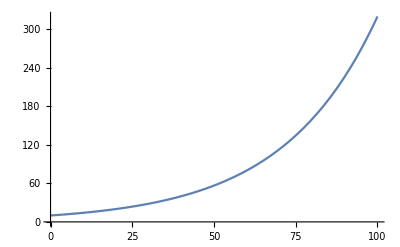

```mathematica
Plot[x[t], {t,0,100}]
```

b. How long does it take for the density to increase to eight times its original value? And to ten times its original value?

```mathematica
Solve[x[t] == 80, t, Reals]
```

{{t→60}}

```mathematica
Solve[x[t] == 100, t, Reals]
N[%]
```

{{t→(20 (Log[2]+Log[5]))/Log[2]}}

{{t→66.4386}}

Fitting linear or exponential to growth data

We have a dataset that we need to fit. 

a. What better describes, i.e. linear or exponential growth, the following data. The data is given in the form {{x,y},...,....}.

myData = {{0.5,1.27},{0.6,6.58},{0.7,7.00},{0.8,8.83},{0.9,8.66},{1.0,5.53},{1.1,9.33},{1.2,14.57},{1.3,8.51},{1.4,17.61},{1.5,12.94},{1.6,18.45},{1.7,19.85},{1.8,25.03},{1.9,28.14},{2.0,28.31},{2.1,33.41},{2.2,41.43},{2.3,40.87},{2.4,56.71},{2.5,59.32}};

Find out by fittings functions, plotting them with the data and finding the error of both fits.



b. What is the differential equation for the fitted function? Also give the numerical values for the parameters.

The SIR model - Seasonal epidemics

With the SIR model you can study how the probability of getting a disease varies with the seasons of the year. SIR stands for Susceptibility - Infection - Recovery and is a set of nonlinear differential equations with periodically varying parameters. The periodically forced SIR model is:

dS/dt=μ-μ S-β(t)I S
dI/dt=β(t)I S-(γ+μ)I
dR/dt=γ I-μ R

Here S, I, and R are the fractions of susceptible, infective, and recovered individuals in the population; μ is the birth and death rate; β(t) is the seasonally dependent infection rate; and γ is the recovery rate. We take β(t) to be periodic; β(t)=β_0[1+sin((2π t)/T)], where T is the length of the infection season and β_0 is a constant. The reproduction number for this system is 1/T∫_0^T (β(t))/(μ+γ)dt; if the integral is greater than one, the disease will not disappear and may undergo interesting and complex phenomena of nonlinear parametric resonance . 
More info can be found here.

a. We want to see how S, I and R change over time with varying parameters. Make a plot (or plots) to analyze how the dynamics change by varying the death rate(μ = 0 - 1), recovery rate(γ= 0 - 1), season length (T= 0 - 30), initial infections rate (β_0= 0 - 1) and the amount of initially infected (I_0).

## References

Information for this notebook was taken from
1. “Mathematica programming: an advanced introduction. Part I: The core language” by Leonid Shifrin.
2. Mathematica main website and documentation.